# Transfer Fit of MC Data

```mathematica
MCFolder="~/ClusterMC_v4/NoMoS_Danfysik_25-02-19_reduceTypes_smallerDV4/";
```

```mathematica
DetHisto=Import[MCFolder<>"GlobalTransferData/"<>"DetXYHistSum.txt","Table"];
```

```mathematica
ListPlot3D[Flatten[Table[
{
DetHisto[[1,i]]+(DetHisto[[1,1]]-DetHisto[[1,2]])/2,
DetHisto[[2,j]]+(DetHisto[[2,1]]-DetHisto[[2,2]])/2,
DetHisto[[2+i,j]]},
{i,1,Length[DetHisto[[1]]]-1},
{j,1,Length[DetHisto[[2]]]-1}
],1],PlotRange->All]
```

-Graphics3D-

### boolean plot to see, where > 0

```mathematica
ListPlot3D[Flatten[Table[
{
DetHisto[[1,i]]+(DetHisto[[1,1]]-DetHisto[[1,2]])/2,
DetHisto[[2,j]]+(DetHisto[[2,1]]-DetHisto[[2,2]])/2,
Boole[DetHisto[[2+i,j]]>0]},
{i,1,Length[DetHisto[[1]]]-1},
{j,1,Length[DetHisto[[2]]]-1}
],1],PlotRange->All]
```

-Graphics3D-

```mathematica
{{ApertXOff,ApertYOff},{ApertX,ApertY},{BDV},{BF},{BA},{BRxB},{BDet}}=Import[MCFolder<>"GlobalTransferData/"<>"OtherParas.txt","Table"]
```

{{0.0301277,1.00623},{0.01,0.035},{0.220899},{0.451107},{0.219769},{0.219722},{0.207816}}

```mathematica
rF=BF/BDV
```

2.04214

```mathematica
rA=BA/BDV
```

0.994887

```mathematica
rRxB=BRxB/BDV
```

0.994674

```mathematica
rDet=BDet/BRxB
```

0.945816

```mathematica
rRxB/rA
```

0.999786

```mathematica
rDet/rRxB
```

0.95088

### grab alpha from blines

```mathematica
AlphaFromBlines=178.20869281586448/180*Pi
```

3.11033

```mathematica
YBlineShiftatDet=-0.016078000000000037;
```

```mathematica
BRxBCenterFromBLines=0.21957007943037976;
```

```mathematica
(BRxBCenterFromBLines-BRxB)/BRxBCenterFromBLines
```

-0.000691704

```mathematica
XAShift=0.0
```

0.

```mathematica
YAShift=0.007188045691239971
```

0.00718805

### we take the “on-top” value

```mathematica
YRxBShift=0.00677284727516161-YAShift
```

-0.000415198

```mathematica
YDetShift=YRxBShift-0.015928000000000164
```

-0.0163432

```mathematica
XRxBShift=0.;
```

```mathematica
XDetShift=0.;
```

### difference is 7e-4. as the MC value is the average over all particles, it doesnt represent the model description. Model needs BRxB in geometric center of beam (actually geometric tube)

### actually, thDet is also different due to alpha not doing 180°!

```mathematica
InfoFile=Import[MCFolder<>"info.txt","Table"];
```

```mathematica
R=InfoFile[[1,2]]
```

0.999002

### also, we havent considered a shift at detector due to field lines shifting..

# Get b0 from raw energy fit

```mathematica
Get["NeutronBeam/ManualShift_NBeamInt.m"]
```

Set::wrsym: Symbol pmax is Protected.

```mathematica
Get["NeutronBeam/XYBinIntBoundaries.m"]
```

```mathematica
EHisto={{0,19550,39100,58650,78200,97750,117300,136850,156400,175950,195500,215050,234600,254150,273700,293250,312800,332350,351900,371450,391000,410550,430100,449650,469200,488750,508300,527850,547400,566950,586500,606050,625600,645150,664700,684250,703800,723350,742900,762450,782000},{346513,594262,752207,876257,976772,1057642,1125859,1180669,1225108,1257819,1280816,1294590,1300669,1294235,1281846,1262522,1235139,1200930,1159120,1116025,1064817,1009259,948177,884889,817021,747223,679132,606469,536427,465628,396264,329609,266697,208156,153816,107114,66949,35323,13249,1940}}
```

{{0,19550,39100,58650,78200,97750,117300,136850,156400,175950,195500,215050,234600,254150,273700,293250,312800,332350,351900,371450,391000,410550,430100,449650,469200,488750,508300,527850,547400,566950,586500,606050,625600,645150,664700,684250,703800,723350,742900,762450,782000},{346513,594262,752207,876257,976772,1057642,1125859,1180669,1225108,1257819,1280816,1294590,1300669,1294235,1281846,1262522,1235139,1200930,1159120,1116025,1064817,1009259,948177,884889,817021,747223,679132,606469,536427,465628,396264,329609,266697,208156,153816,107114,66949,35323,13249,1940}}

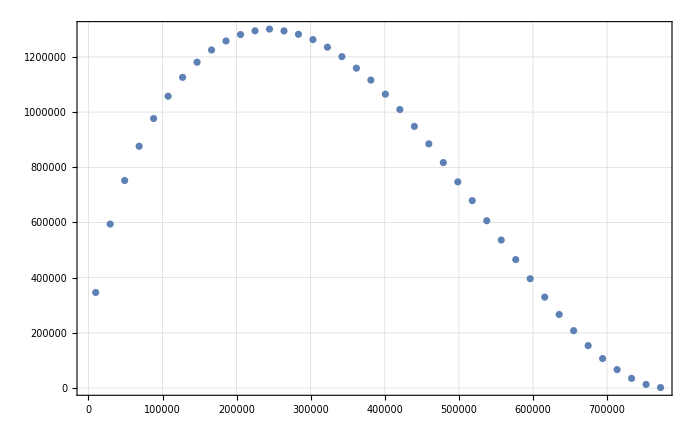

```mathematica
ListPlot[Transpose[{EHisto[[1,1;;-2]]+EHisto[[1,2]]/2,Around[#,Sqrt[#]]&/@EHisto[[2]]}]]
```

```mathematica
FitData=Table[{bin,EHisto[[2,bin]]},{bin,1,Length[EHisto[[2]]]}]
```

{{1,346513},{2,594262},{3,752207},{4,876257},{5,976772},{6,1057642},{7,1125859},{8,1180669},{9,1225108},{10,1257819},{11,1280816},{12,1294590},{13,1300669},{14,1294235},{15,1281846},{16,1262522},{17,1235139},{18,1200930},{19,1159120},{20,1116025},{21,1064817},{22,1009259},{23,948177},{24,884889},{25,817021},{26,747223},{27,679132},{28,606469},{29,536427},{30,465628},{31,396264},{32,329609},{33,266697},{34,208156},{35,153816},{36,107114},{37,66949},{38,35323},{39,13249},{40,1940}}

```mathematica
GlobalStat=Total[EHisto[[2]]]
```

31157159

```mathematica
CloseKernels[]
LaunchKernels[]
```

{}

{KernelObject[1,10.4.85.27],KernelObject[2,10.4.85.27],KernelObject[3,10.4.85.27],KernelObject[4,10.4.85.27],KernelObject[5,10.4.85.27],KernelObject[6,10.4.85.27],KernelObject[7,local],KernelObject[8,local],KernelObject[9,local],KernelObject[10,local]}

```mathematica
ClearAll[eSpectrumBinned]
```

```mathematica
eSpectrumBinned[b_?NumericQ]:=eSpectrumBinned[b]=GlobalStat*ParallelTable[
NIntegrate[weNormed[λ0,κ0,b,Ee],{Ee,me+EHisto[[1,bin]],me+EHisto[[1,bin+1]]},PrecisionGoal->6],{bin,1,Length[EHisto[[1]]]-1}]
```

```mathematica
ClearAll[eSpectrumBin]
```

```mathematica
eSpectrumBin[b_?NumericQ,bin_?NumericQ]:=eSpectrumBinned[b][[bin]]
```

```mathematica
eSpectrumBin[0.,1]
```

345381.

```mathematica
Total[Table[eSpectrumBin[0.,bin],{bin,1,Length[EHisto[[1]]]-1}]]
```

3.11572×10^7

```mathematica
rawSpecFit=NonlinearModelFit[
FitData,
{eSpectrumBin[b,bin],-0.6<b<0.6},
{{b,0.5}},
bin,
Method->"NMinimize",PrecisionGoal->6
]
```

FittedModel[eSpectrumBin[-0.000324095,bin]]

### takes 6 min

```mathematica
rawSpecFit["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
b | -0.000324095 | 0.00121154 | -0.267506 | 0.790489

### now with statistical weights included

```mathematica
rawSpecFitWeights=NonlinearModelFit[
FitData,
{eSpectrumBin[b,bin],-0.005<b<0.005},
{{b,0.0001}},
bin,Weights->1/FitData[[All,2]],VarianceEstimatorFunction->(1&),
Method->"NMinimize",PrecisionGoal->6
]
```

FittedModel[eSpectrumBin[-0.0000338262,bin]]

```mathematica
365/60.
```

6.08333

### takes 6 min

```mathematica
rawSpecFitWeights["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
b | -0.0000338262 | 0.00134066 | -0.025231 | 0.979999

```mathematica
rawSpecFitWeights["BestFitParameters"][[1,2]]//ScientificForm
```

-3.38262×10^-5

```mathematica
Sqrt[GlobalStat]*0.00134
```

7.47969

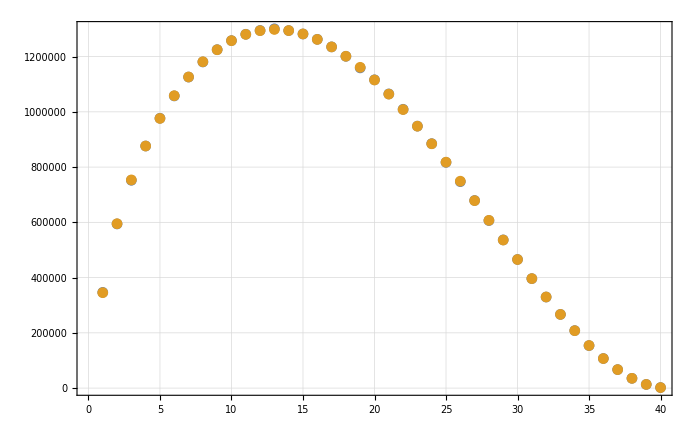

```mathematica
ListPlot[{FitData,Table[rawSpecFitWeights[bin],{bin,1,40}]}]
```

## Get the transfer function

### calculate bins, choose binsize, multiple of MCData binning

### plot original grid

```mathematica
-(DetHisto[[1,1]]-DetHisto[[1,2]])
```

0.005

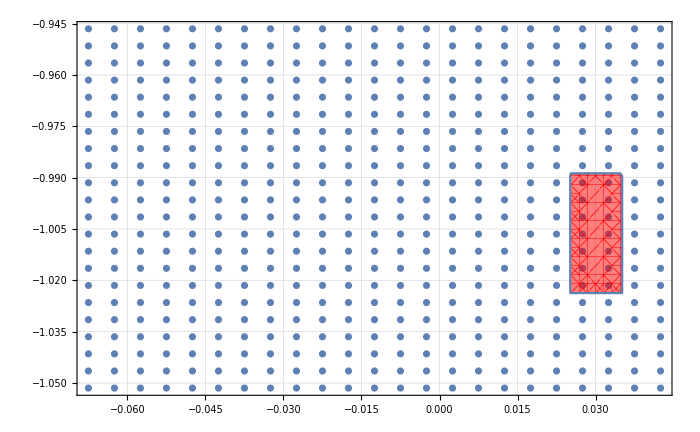

```mathematica
Show[
ListPlot[
Flatten[Table[
{
DetHisto[[1,i]]+(DetHisto[[1,2]]-DetHisto[[1,1]])/2,
DetHisto[[2,j]]+(DetHisto[[2,2]]-DetHisto[[2,1]])/2
},
{i,1,Length[DetHisto[[1]]]-1},
{j,1,Length[DetHisto[[2]]]-1}],1],PlotRange->All],
RegionPlot[Abs[x-ApertXOff]<ApertX/2&&Abs[y+ApertYOff]<ApertY/2,{x,0,0.06},{y,-1.05,-0.95},PlotStyle->Directive[Red,Opacity[0.5]]]
]
```

```mathematica
?XYBinIntBoundaries
```

### we can directly get a XYBin form from original table, even being able to jump over steps by 2 e.g.

```mathematica
XYBinBoundariesOriginal=Flatten[Table[
{
{DetHisto[[1,xi]],DetHisto[[1,xi+1]]},
{-DetHisto[[2,yi]]-R,-DetHisto[[2,yi+1]]-R}
},{xi,1,Length[DetHisto[[1]]]-1},{yi,1,Length[DetHisto[[2]]]-1}],1];
```

```mathematica
XYBinBoundariesOriginal//Length
```

506

### half bins

```mathematica
XYBinBoundariesHalf=Flatten[Table[
{
{DetHisto[[1,xi]],DetHisto[[1,xi+2]]},
{-DetHisto[[2,yi+2]]-R,-DetHisto[[2,yi]]-R}
},{xi,2,Length[DetHisto[[1]]]-1,2},{yi,1,Length[DetHisto[[2]]]-1,2}],1];
```

### we start for x at index 2 for shift, also because that area is 0 anyway

```mathematica
XYBinBoundariesHalf//Length
```

121

```mathematica
(506-22)/4.
```

121.

```mathematica
XYBinBoundariesHalf
```

{{{-0.065,-0.055},{0.045,0.055}},{{-0.065,-0.055},{0.035,0.045}},{{-0.065,-0.055},{0.025,0.035}},{{-0.065,-0.055},{0.015,0.025}},{{-0.065,-0.055},{0.005,0.015}},{{-0.065,-0.055},{-0.005,0.005}},{{-0.065,-0.055},{-0.015,-0.005}},{{-0.065,-0.055},{-0.025,-0.015}},{{-0.065,-0.055},{-0.035,-0.025}},{{-0.065,-0.055},{-0.045,-0.035}},{{-0.065,-0.055},{-0.055,-0.045}},{{-0.055,-0.045},{0.045,0.055}},{{-0.055,-0.045},{0.035,0.045}},{{-0.055,-0.045},{0.025,0.035}},{{-0.055,-0.045},{0.015,0.025}},{{-0.055,-0.045},{0.005,0.015}},{{-0.055,-0.045},{-0.005,0.005}},{{-0.055,-0.045},{-0.015,-0.005}},{{-0.055,-0.045},{-0.025,-0.015}},{{-0.055,-0.045},{-0.035,-0.025}},{{-0.055,-0.045},{-0.045,-0.035}},{{-0.055,-0.045},{-0.055,-0.045}},{{-0.045,-0.035},{0.045,0.055}},{{-0.045,-0.035},{0.035,0.045}},{{-0.045,-0.035},{0.025,0.035}},{{-0.045,-0.035},{0.015,0.025}},{{-0.045,-0.035},{0.005,0.015}},{{-0.045,-0.035},{-0.005,0.005}},{{-0.045,-0.035},{-0.015,-0.005}},{{-0.045,-0.035},{-0.025,-0.015}},{{-0.045,-0.035},{-0.035,-0.025}},{{-0.045,-0.035},{-0.045,-0.035}},{{-0.045,-0.035},{-0.055,-0.045}},{{-0.035,-0.025},{0.045,0.055}},{{-0.035,-0.025},{0.035,0.045}},{{-0.035,-0.025},{0.025,0.035}},{{-0.035,-0.025},{0.015,0.025}},{{-0.035,-0.025},{0.005,0.015}},{{-0.035,-0.025},{-0.005,0.005}},{{-0.035,-0.025},{-0.015,-0.005}},{{-0.035,-0.025},{-0.025,-0.015}},{{-0.035,-0.025},{-0.035,-0.025}},{{-0.035,-0.025},{-0.045,-0.035}},{{-0.035,-0.025},{-0.055,-0.045}},{{-0.025,-0.015},{0.045,0.055}},{{-0.025,-0.015},{0.035,0.045}},{{-0.025,-0.015},{0.025,0.035}},{{-0.025,-0.015},{0.015,0.025}},{{-0.025,-0.015},{0.005,0.015}},{{-0.025,-0.015},{-0.005,0.005}},{{-0.025,-0.015},{-0.015,-0.005}},{{-0.025,-0.015},{-0.025,-0.015}},{{-0.025,-0.015},{-0.035,-0.025}},{{-0.025,-0.015},{-0.045,-0.035}},{{-0.025,-0.015},{-0.055,-0.045}},{{-0.015,-0.005},{0.045,0.055}},{{-0.015,-0.005},{0.035,0.045}},{{-0.015,-0.005},{0.025,0.035}},{{-0.015,-0.005},{0.015,0.025}},{{-0.015,-0.005},{0.005,0.015}},{{-0.015,-0.005},{-0.005,0.005}},{{-0.015,-0.005},{-0.015,-0.005}},{{-0.015,-0.005},{-0.025,-0.015}},{{-0.015,-0.005},{-0.035,-0.025}},{{-0.015,-0.005},{-0.045,-0.035}},{{-0.015,-0.005},{-0.055,-0.045}},{{-0.005,0.005},{0.045,0.055}},{{-0.005,0.005},{0.035,0.045}},{{-0.005,0.005},{0.025,0.035}},{{-0.005,0.005},{0.015,0.025}},{{-0.005,0.005},{0.005,0.015}},{{-0.005,0.005},{-0.005,0.005}},{{-0.005,0.005},{-0.015,-0.005}},{{-0.005,0.005},{-0.025,-0.015}},{{-0.005,0.005},{-0.035,-0.025}},{{-0.005,0.005},{-0.045,-0.035}},{{-0.005,0.005},{-0.055,-0.045}},{{0.005,0.015},{0.045,0.055}},{{0.005,0.015},{0.035,0.045}},{{0.005,0.015},{0.025,0.035}},{{0.005,0.015},{0.015,0.025}},{{0.005,0.015},{0.005,0.015}},{{0.005,0.015},{-0.005,0.005}},{{0.005,0.015},{-0.015,-0.005}},{{0.005,0.015},{-0.025,-0.015}},{{0.005,0.015},{-0.035,-0.025}},{{0.005,0.015},{-0.045,-0.035}},{{0.005,0.015},{-0.055,-0.045}},{{0.015,0.025},{0.045,0.055}},{{0.015,0.025},{0.035,0.045}},{{0.015,0.025},{0.025,0.035}},{{0.015,0.025},{0.015,0.025}},{{0.015,0.025},{0.005,0.015}},{{0.015,0.025},{-0.005,0.005}},{{0.015,0.025},{-0.015,-0.005}},{{0.015,0.025},{-0.025,-0.015}},{{0.015,0.025},{-0.035,-0.025}},{{0.015,0.025},{-0.045,-0.035}},{{0.015,0.025},{-0.055,-0.045}},{{0.025,0.035},{0.045,0.055}},{{0.025,0.035},{0.035,0.045}},{{0.025,0.035},{0.025,0.035}},{{0.025,0.035},{0.015,0.025}},{{0.025,0.035},{0.005,0.015}},{{0.025,0.035},{-0.005,0.005}},{{0.025,0.035},{-0.015,-0.005}},{{0.025,0.035},{-0.025,-0.015}},{{0.025,0.035},{-0.035,-0.025}},{{0.025,0.035},{-0.045,-0.035}},{{0.025,0.035},{-0.055,-0.045}},{{0.035,0.045},{0.045,0.055}},{{0.035,0.045},{0.035,0.045}},{{0.035,0.045},{0.025,0.035}},{{0.035,0.045},{0.015,0.025}},{{0.035,0.045},{0.005,0.015}},{{0.035,0.045},{-0.005,0.005}},{{0.035,0.045},{-0.015,-0.005}},{{0.035,0.045},{-0.025,-0.015}},{{0.035,0.045},{-0.035,-0.025}},{{0.035,0.045},{-0.045,-0.035}},{{0.035,0.045},{-0.055,-0.045}}}

### calculate first transfer spectrum with the rough parameters

```mathematica
IntMethod={"GlobalAdaptive",Method->"MultidimensionalRule"};
```

```mathematica
XYBinBoundariesHalf[[72]]
```

{{-0.005,0.005},{0.005,-0.005}}

```mathematica
XYBinBoundariesHalf[[100]]
```

{{0.025,0.035},{0.055,0.045}}

```mathematica
BinIntShift[0.,XYBinBoundariesHalf[[72]],{AlphaFromBlines,BRxBCenterFromBLines,rF,rRxB,rA,rDet,R,1.,1.},{XAShift,YAShift,XDetShift,YDetShift},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,-0.03,0.},
{IntMethod,3,3,0,2},{IntMethod,3,3,0,2},{IntMethod,3,3,0,0}
]
```

-8.04197×10^-6

```mathematica
BinIntShift[0.,XYBinBoundariesHalf[[72]],{AlphaFromBlines,BRxBCenterFromBLines,rF,rRxB,rA,rDet,R,1.,1.},{0,0,0,0},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,-0.03,0.},
{IntMethod,3,3,0,2},{IntMethod,3,3,0,2},{IntMethod,3,3,0,0}
]
```

-7.88184×10^-6

```mathematica
BinIntShift[0.,XYBinBoundariesHalf[[100]],{AlphaFromBlines,BRxBCenterFromBLines,rF,rRxB,rA,rDet,R,1.,1.},{XAShift,YAShift,XDetShift,YDetShift},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,-0.03,0.},
{IntMethod,3,3,0,2},{IntMethod,3,3,0,2},{IntMethod,3,3,0,0}
]
```

0.

```mathematica
BinIntShift[0.,XYBinBoundariesHalf[[100]],{AlphaFromBlines,BRxBCenterFromBLines,rF,rRxB,rA,rDet,R,1.,1.},{0,0,0,0},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,-0.03,0.},
{IntMethod,3,3,0,2},{IntMethod,3,3,0,2},{IntMethod,3,3,0,0}
]
```

0.

```mathematica
CloseKernels[]
LaunchKernels[]
```

{}

```mathematica
result1=ParallelMap[BinIntShift[0.,#,{AlphaFromBlines,BRxBCenterFromBLines,rF,rRxB,rA,rDet,R,1.,1.},{XAShift,YAShift,XDetShift,YDetShift},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,-0.03,0.},
{IntMethod,3,3,0,2},{IntMethod,3,3,0,2},{IntMethod,3,3,0,0}
]&,XYBinBoundariesHalf[[1;;8]]]
```

{0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
result2=ParallelMap[BinIntShift[0.,#,{AlphaFromBlines,BRxBCenterFromBLines,rF,rRxB,rA,rDet,R,1.,1.},{XAShift,YAShift,XDetShift,YDetShift},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,-0.03,0.},
{IntMethod,3,3,0,2},{IntMethod,3,3,0,2},{IntMethod,3,3,0,0}
]&,XYBinBoundariesHalf[[9;;24]]]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
result3=ParallelMap[BinIntShift[0.,#,{AlphaFromBlines,BRxBCenterFromBLines,rF,rRxB,rA,rDet,R,1.,1.},{XAShift,YAShift,XDetShift,YDetShift},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,-0.03,0.},
{IntMethod,3,3,0,2},{IntMethod,3,3,0,2},{IntMethod,3,3,0,0}
]&,XYBinBoundariesHalf[[25;;48]]]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.51905×10^-8,-3.7533×10^-7,-3.82886×10^-7,-3.90672×10^-7,-1.47494×10^-7,0.,0.,0.,0.,0.,0.,-1.62006×10^-7,-2.27099×10^-6}

```mathematica
result4=ParallelMap[BinIntShift[0.,#,{AlphaFromBlines,BRxBCenterFromBLines,rF,rRxB,rA,rDet,R,1.,1.},{XAShift,YAShift,XDetShift,YDetShift},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,-0.03,0.},
{IntMethod,3,3,0,2},{IntMethod,3,3,0,2},{IntMethod,3,3,0,0}
]&,XYBinBoundariesHalf[[49;;96]]]
```

{-2.31736×10^-6,-2.36518×10^-6,-9.4873×10^-7,0.,0.,0.,0.,0.,0.,-3.37286×10^-7,-4.73284×10^-6,-4.83499×10^-6,-4.94056×10^-6,-1.98274×10^-6,0.,0.,0.,0.,0.,0.,-5.47368×10^-7,-7.68426×10^-6,-7.86107×10^-6,-8.04413×10^-6,-3.23241×10^-6,0.,0.,0.,0.,0.,0.,-8.02277×10^-7,-0.0000112669,-0.0000115392,-0.0000118215,-4.75528×10^-6,0.,0.,0.,0.,0.,0.,-1.1224×10^-6,-0.0000155181,-0.0000159069,-0.0000163102,-6.56589×10^-6,0.}

### took 239s

```mathematica
result5=ParallelMap[BinIntShift[0.,#,{AlphaFromBlines,BRxBCenterFromBLines,rF,rRxB,rA,rDet,R,1.,1.},{XAShift,YAShift,XDetShift,YDetShift},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,-0.03,0.},
{IntMethod,3,3,0,2},{IntMethod,3,3,0,2},{IntMethod,3,3,0,0}
]&,XYBinBoundariesHalf[[97;;-1]]]
```

{0.,0.,0.,0.,0.,-1.56417×10^-6,-0.000020448,-0.0000209741,-0.00002152,-8.66804×10^-6,0.,0.,0.,0.,0.,0.,-2.12883×10^-6,-0.0000260592,-0.0000267431,-0.0000274532,-0.0000110626,0.,0.,0.,0.}

### took 107s

```mathematica
result=Abs[Join[result1,result2,result3,result4,result5]]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.51905×10^-8,3.7533×10^-7,3.82886×10^-7,3.90672×10^-7,1.47494×10^-7,0.,0.,0.,0.,0.,0.,1.62006×10^-7,2.27099×10^-6,2.31736×10^-6,2.36518×10^-6,9.4873×10^-7,0.,0.,0.,0.,0.,0.,3.37286×10^-7,4.73284×10^-6,4.83499×10^-6,4.94056×10^-6,1.98274×10^-6,0.,0.,0.,0.,0.,0.,5.47368×10^-7,7.68426×10^-6,7.86107×10^-6,8.04413×10^-6,3.23241×10^-6,0.,0.,0.,0.,0.,0.,8.02277×10^-7,0.0000112669,0.0000115392,0.0000118215,4.75528×10^-6,0.,0.,0.,0.,0.,0.,1.1224×10^-6,0.0000155181,0.0000159069,0.0000163102,6.56589×10^-6,0.,0.,0.,0.,0.,0.,1.56417×10^-6,0.000020448,0.0000209741,0.00002152,8.66804×10^-6,0.,0.,0.,0.,0.,0.,2.12883×10^-6,0.0000260592,0.0000267431,0.0000274532,0.0000110626,0.,0.,0.,0.}

```mathematica
result=result/Total[result]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000079764,0.00118846,0.00121238,0.00123704,0.000467028,0.,0.,0.,0.,0.,0.,0.000512981,0.00719093,0.00733774,0.00748917,0.00300408,0.,0.,0.,0.,0.,0.,0.00106799,0.0149862,0.0153096,0.0156439,0.00627822,0.,0.,0.,0.,0.,0.,0.0017332,0.0243316,0.0248915,0.0254711,0.0102352,0.,0.,0.,0.,0.,0.,0.00254035,0.0356757,0.0365381,0.037432,0.0150573,0.,0.,0.,0.,0.,0.,0.003554,0.0491369,0.0503681,0.051645,0.0207904,0.,0.,0.,0.,0.,0.,0.00495284,0.0647471,0.0664129,0.0681414,0.0274467,0.,0.,0.,0.,0.,0.,0.00674078,0.0825144,0.0846803,0.0869285,0.0350289,0.,0.,0.,0.}

```mathematica
XYBinCentersHalf=BinCenters[XYBinBoundariesHalf];
```

```mathematica
ListPlot3D[Flatten[Table[
{
DetHisto[[1,i]]+(DetHisto[[1,1]]-DetHisto[[1,2]])/2,
DetHisto[[2,j]]+(DetHisto[[2,1]]-DetHisto[[2,2]])/2,
DetHisto[[2+i,j]]},
{i,1,Length[DetHisto[[1]]]-1},
{j,1,Length[DetHisto[[2]]]-1}
],1],PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[Transpose[{XYBinCentersHalf[[All,1]],XYBinCentersHalf[[All,2]],result}],PlotRange->All,AxesLabel->{"x","y","#"}]
```

-Graphics3D-

```mathematica
BRxBCenterFromBLines
```

0.21957

```mathematica
AlphaFromBlines
```

178.209

```mathematica
result6=ParallelMap[BinIntShift[0.,#,{AlphaFromBlines,BRxBCenterFromBLines,rF,rRxB,rA,rDet,R,1.,1.},{0.,0.,0.,0.},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,-0.03,0.},
{IntMethod,3,3,0,2},{IntMethod,3,3,0,2},{IntMethod,3,3,0,0}
]&,XYBinBoundariesHalf[[1;;-1]]]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-9.67505×10^-8,-3.76126×10^-7,-3.83708×10^-7,-3.91385×10^-7,-1.03199×10^-7,0.,0.,0.,0.,0.,0.,-5.54159×10^-7,-2.2758×10^-6,-2.32233×10^-6,-2.36891×10^-6,-5.91325×10^-7,0.,0.,0.,0.,0.,0.,-1.15457×10^-6,-4.7431×10^-6,-4.84562×10^-6,-4.9456×10^-6,-1.23537×10^-6,0.,0.,0.,0.,0.,0.,-1.87263×10^-6,-7.70144×10^-6,-7.87892×10^-6,-8.04744×10^-6,-2.01051×10^-6,0.,0.,0.,0.,0.,0.,-2.74327×10^-6,-0.0000112925,-0.0000115659,-0.0000118186,-2.95272×10^-6,0.,0.,0.,0.,0.,0.,-3.77583×10^-6,-0.0000155535,-0.0000159437,-0.0000162947,-4.07066×10^-6,0.,0.,0.,0.,0.,0.,-4.9728×10^-6,-0.0000204943,-0.0000210223,-0.0000214836,-5.36605×10^-6,0.,0.,0.,0.,0.,0.,-6.33476×10^-6,-0.0000261173,-0.0000268037,-0.0000273859,-6.8387×10^-6,0.,0.,0.}

### took 378s

```mathematica
fullresult=ParallelMap[BinIntShift[0.,#,{AlphaFromBlines,BRxBCenterFromBLines,rF,rRxB,rA,rDet,R,1.,1.},{XAShift,YAShift,XDetShift,YDetShift},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,-0.03,0.},
{IntMethod,3,3,0,2},{IntMethod,3,3,0,2},{IntMethod,3,3,0,0}
]&,XYBinBoundariesHalf]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 0 recursive bisections in yD near {xD,yD} = {-0.00655876,-0.00655876}. NIntegrate obtained 0.0772783 and 0.00390439 for the integral and error estimates.

$Aborted

```mathematica
result1noShift=ParallelMap[BinIntShift[0.,#,{AlphaFromBlines,BRxBCenterFromBLines,rF,rRxB,rA,rDet,R,1.,1.},{0.,0.,0.,0.},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,-0.03,0.},
{IntMethod,3,3,0,2},{IntMethod,3,3,0,2},{IntMethod,3,3,0,0}
]&,XYBinBoundariesHalf[[1;;8]]]
```

{0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
result2noShift=ParallelMap[BinIntShift[0.,#,{AlphaFromBlines,BRxBCenterFromBLines,rF,rRxB,rA,rDet,R,1.,1.},{0.,0.,0.,0.},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,-0.03,0.},
{IntMethod,3,3,0,2},{IntMethod,3,3,0,2},{IntMethod,3,3,0,0}
]&,XYBinBoundariesHalf[[9;;24]]]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
result3noShift=ParallelMap[BinIntShift[0.,#,{AlphaFromBlines,BRxBCenterFromBLines,rF,rRxB,rA,rDet,R,1.,1.},{0.,0.,0.,0.},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,-0.03,0.},
{IntMethod,3,3,0,2},{IntMethod,3,3,0,2},{IntMethod,3,3,0,0}
]&,XYBinBoundariesHalf[[25;;48]]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 0 recursive bisections in yD near {xD,yD} = {-0.0165588,0.0234412}. NIntegrate obtained 0.0204141 and 0.00175137 for the integral and error estimates.

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0017224,0.00697337,0.00720302,0.00742299,0.00186162,0.,0.,0.,0.,0.,0.,0.0204141}

### took 1911s

```mathematica
result4noShift=ParallelMap[BinIntShift[0.,#,{AlphaFromBlines,BRxBCenterFromBLines,rF,rRxB,rA,rDet,R,1.,1.},{0.,0.,0.,0.},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,-0.03,0.},
{IntMethod,3,3,0,2},{IntMethod,3,3,0,2},{IntMethod,3,3,0,0}
]&,XYBinBoundariesHalf[[49;;-1]]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 0 recursive bisections in yD near {xD,yD} = {-0.00655876,0.0234412}. NIntegrate obtained 0.0558975 and 0.00154789 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 0 recursive bisections in yD near {xD,yD} = {0.00344124,-0.0165588}. NIntegrate obtained 0.070927 and 0.00102255 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 0 recursive bisections in xD near {xD,yD} = {-0.0165588,-0.0165588}. NIntegrate obtained 0.0217753 and 0.00185281 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 0 recursive bisections in xD near {xD,yD} = {0.0134412,-0.0165588}. NIntegrate obtained 0.0489032 and 0.00165595 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 0 recursive bisections in yD near {xD,yD} = {-0.00655876,-0.0165588}. NIntegrate obtained 0.057842 and 0.00269411 for the integral and error estimates.

{0.0759364,0.0794628,0.079605,0.0217753,2.50389×10^-6,0.,0.,0.,0.,0.000558431,0.0558975,0.175199,0.188974,0.17875,0.057842,0.000800497,0.,0.,0.,0.,0.00402856,0.0719248,0.194488,0.216768,0.192573,0.070927,0.00471147,0.,0.,0.,2.92357×10^-6,0.00617405,0.0528434,0.129937,0.145667,0.124314,0.0489032,0.00621044,0.0000268213,0.,0.,0.0000535286,0.00384691,0.0231713,0.0517016,0.0576115,0.0471118,0.0198883,0.00338506,0.0000414229,0.,0.,0.0000132037,0.00121478,0.00583971,0.0116256,0.0130965,0.010179,0.00466839,0.000870961,0.,0.,0.,0.,0.000134329,0.000855881,0.00164632,0.00182249,0.00137698,0.000607149,0.0000645132,0.,0.}

### took 15646s or 4.4h

### following is the full transfer spectrum with 0 for the manual shifts

```mathematica
resultfull=ParallelMap[AbsoluteTiming[BinIntShift[0.,#,{AlphaFromBlines,BRxBCenterFromBLines,rF,rRxB,rA,rDet,R,1.,1.},{0.,0.,0.,0.},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,-0.03,0.},
{IntMethod,3,3,0,2},{IntMethod,3,3,0,2},{IntMethod,3,3,0,0}
]]&,XYBinBoundariesHalf[[1;;-1]]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 0 recursive bisections in xD near {xD,yD} = {-0.0165588,-0.0165588}. NIntegrate obtained 0.0217753 and 0.00185281 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 0 recursive bisections in yD near {xD,yD} = {-0.0165588,0.0234412}. NIntegrate obtained 0.0204141 and 0.00175137 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 0 recursive bisections in yD near {xD,yD} = {-0.00655876,0.0234412}. NIntegrate obtained 0.0558975 and 0.00154789 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 0 recursive bisections in yD near {xD,yD} = {-0.00655876,-0.0165588}. NIntegrate obtained 0.057842 and 0.00269411 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 0 recursive bisections in yD near {xD,yD} = {0.00344124,-0.0165588}. NIntegrate obtained 0.070927 and 0.00102255 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 0 recursive bisections in xD near {xD,yD} = {0.0134412,-0.0165588}. NIntegrate obtained 0.0489032 and 0.00165595 for the integral and error estimates.

{{10.8146,0.},{10.8049,0.},{11.5755,0.},{12.1374,0.},{11.8688,0.},{12.308,0.},{13.3175,0.},{12.3887,0.},{12.1104,0.},{11.8074,0.},{11.9575,0.},{11.8999,0.},{12.0312,0.},{12.8359,0.},{13.0133,0.},{12.9967,0.},{12.0603,0.},{11.6984,0.},{10.9053,0.},{10.6652,0.},{10.7256,0.},{16.8608,0.},{15.4328,0.},{15.5357,0.},{16.4197,0.},{17.5229,0.},{19.0554,0.},{17.5665,0.},{16.7158,0.},{15.629,0.},{15.5796,0.},{15.7289,0.},{15.5085,0.},{25.7536,0.},{25.872,0.},{25.1059,0.},{596.9,0.0017224},{777.323,0.00697337},{593.597,0.00720302},{743.924,0.00742299},{614.318,0.00186162},{16.6944,0.},{16.696,0.},{16.8213,0.},{21.7628,0.},{21.7017,0.},{25.5426,0.},{1377.24,0.0204141},{1303.32,0.0759364},{664.585,0.0794628},{1181.64,0.079605},{1369.68,0.0217753},{47.3473,2.50389×10^-6},{22.605,0.},{22.8082,0.},{23.0329,0.},{22.9695,0.},{219.335,0.000558431},{2201.04,0.0558975},{1687.49,0.175199},{699.941,0.188974},{2868.8,0.17875},{2569.33,0.057842},{471.423,0.000800497},{32.6211,0.},{31.2725,0.},{31.9923,0.},{31.9014,0.},{1089.56,0.00402856},{3782.21,0.0719248},{4280.96,0.194488},{2100.45,0.216768},{4617.6,0.192573},{2556.7,0.070927},{1000.13,0.00471147},{29.2921,0.},{22.5607,0.},{22.5519,0.},{36.5353,2.92357×10^-6},{1255.28,0.00617405},{2675.41,0.0528434},{3621.23,0.129937},{3750.15,0.145667},{3861.73,0.124314},{2435.02,0.0489032},{1023.98,0.00621044},{159.238,0.0000268213},{30.2622,0.},{29.7322,0.},{209.663,0.0000535286},{1791.78,0.00384691},{2070.28,0.0231713},{2584.41,0.0517016},{3148.96,0.0576115},{2420.24,0.0471118},{1510.6,0.0198883},{1010.97,0.00338506},{132.102,0.0000414229},{20.0683,0.},{17.1334,0.},{89.9959,0.0000132037},{879.665,0.00121478},{1272.55,0.00583971},{1839.43,0.0116256},{2410.31,0.0130965},{1851.42,0.010179},{1626.64,0.00466839},{745.032,0.000870961},{16.944,0.},{16.7219,0.},{12.8213,0.},{9.39133,0.},{230.796,0.000134329},{860.758,0.000855881},{1168.68,0.00164632},{1449.62,0.00182249},{1719.81,0.00137698},{1027.73,0.000607149},{308.589,0.0000645132},{11.6074,0.},{11.6271,0.}}

### took 16240s or 4.5h

```mathematica
CloseKernels[]
LaunchKernels[]
```

{KernelObject[28,10.4.85.27,<defunct>],KernelObject[29,10.4.85.27,<defunct>],KernelObject[30,10.4.85.27,<defunct>],KernelObject[31,10.4.85.43,<defunct>],KernelObject[32,10.4.85.43,<defunct>],KernelObject[33,local,<defunct>],KernelObject[34,local,<defunct>],KernelObject[35,local,<defunct>],KernelObject[36,local,<defunct>]}

{KernelObject[37,10.4.85.27],KernelObject[38,10.4.85.27],KernelObject[39,10.4.85.27],KernelObject[40,10.4.85.27],KernelObject[41,10.4.85.43],KernelObject[42,10.4.85.43],KernelObject[43,local],KernelObject[44,local],KernelObject[45,local],KernelObject[46,local]}

```mathematica
resultfullwShiftPrec4=ParallelMap[AbsoluteTiming[BinIntShift[0.,#,{AlphaFromBlines,BRxBCenterFromBLines,rF,rRxB,rA,rDet,R,1.,1.},{XAShift,YAShift,XDetShift,YDetShift},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,-0.03,0.},
{IntMethod,4,3,0,2},{IntMethod,3,3,0,2},{IntMethod,3,3,0,0}
]]&,XYBinBoundariesHalf,Method->"FinestGrained"]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 0 recursive bisections in yD near {xD,yD} = {-0.0165588,-0.00655876}. NIntegrate obtained 0.0313363 and 0.00284473 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 0 recursive bisections in yD near {xD,yD} = {-0.00655876,-0.00655876}. NIntegrate obtained 0.0772838 and 0.00391351 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 0 recursive bisections in yD near {xD,yD} = {0.00344124,-0.00655876}. NIntegrate obtained 0.0905995 and 0.00317188 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 0 recursive bisections in yD near {xD,yD} = {0.0134412,-0.00655876}. NIntegrate obtained 0.0618846 and 0.00170108 for the integral and error estimates.

{{11.5073,0.},{11.9706,0.},{12.6356,0.},{12.9402,0.},{34.5537,0.},{35.2485,0.},{16.5812,0.},{16.7029,0.},{14.773,0.},{15.2796,0.},{11.6624,0.},{12.053,0.},{11.9136,0.},{12.7653,0.},{16.9408,0.},{16.6682,0.},{18.1377,0.},{17.1758,0.},{12.0322,0.},{12.3022,0.},{12.086,0.},{11.9782,0.},{15.6263,0.},{16.1819,0.},{17.4799,0.},{30.4165,0.},{18.286,0.},{30.4652,0.},{13.7792,0.},{12.8801,0.},{12.429,0.},{12.4552,0.},{15.7897,0.},{24.7127,0.},{19.2473,0.},{448.611,0.00084068},{686.18,0.00675595},{433.328,0.00702438},{554.831,0.00724899},{846.718,0.00277285},{24.8279,0.},{42.708,0.},{42.9179,0.},{18.9447,0.},{32.3213,0.},{25.0237,0.},{1858.19,0.0120124},{1710.04,0.0725505},{1413.93,0.0777349},{1965.13,0.0793213},{2151.66,0.0313363},{141.346,0.000047925},{25.5477,0.},{25.5939,0.},{25.5459,0.},{25.9569,0.},{250.031,0.000213618},{3399.42,0.0380285},{2628.53,0.166532},{920.689,0.186217},{1782.,0.18319},{4015.71,0.0772838},{1999.64,0.00204877},{25.9676,0.},{25.9329,0.},{26.2859,0.},{26.7279,0.},{625.602,0.00215425},{4247.59,0.0541021},{5804.32,0.186017},{3619.68,0.215772},{3570.98,0.201357},{4348.28,0.0905995},{1469.58,0.00723233},{56.2088,3.28974×10^-6},{26.0783,0.},{26.0145,0.},{40.519,9.34087×10^-7},{1434.81,0.00411925},{6604.09,0.0426776},{6626.34,0.126016},{2373.51,0.14753},{4075.78,0.132049},{4201.71,0.0618846},{4498.54,0.00853171},{354.89,0.000118213},{32.5478,0.},{31.9788,0.},{187.975,0.0000156092},{1702.81,0.00290607},{3000.02,0.0198387},{3439.69,0.0512658},{3243.95,0.0597785},{3611.36,0.051341},{2367.14,0.0248082},{2089.05,0.00455286},{657.058,0.000158062},{26.9951,0.},{27.3194,0.},{118.332,7.42057×10^-6},{1541.56,0.00096838},{1853.7,0.00541188},{1892.08,0.0117921},{2214.62,0.0139355},{4136.03,0.0114482},{3220.92,0.00575869},{915.264,0.00124585},{177.14,0.0000352288},{17.8321,0.},{17.7427,0.},{14.0887,0.},{312.873,0.000113021},{914.442,0.000823173},{1919.41,0.00172405},{1874.41,0.00200604},{1092.71,0.00159223},{1455.76,0.00077208},{683.669,0.000132563},{9.16971,0.},{9.53831,0.},{8.92989,0.}}

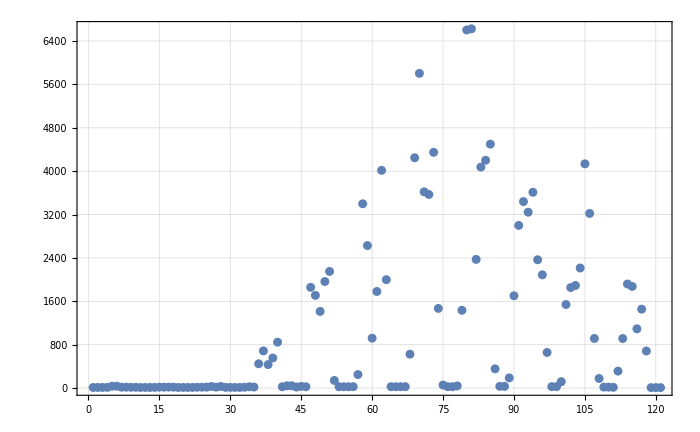

```mathematica
ListPlot[resultfullwShiftPrec4[[All,1]]]
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersHalf[[All,1]],XYBinCentersHalf[[All,2]],resultfullwShiftPrec4[[All,2]]}],PlotRange->All,AxesLabel->{"x","y","#"}]
```

-Graphics3D-

### now we still have to adopt the MC data to half binning

```mathematica
DetHistoBinHalfEntries=Flatten[Table[
DetHisto[[2+i,j]]+DetHisto[[2+i,j+1]]+DetHisto[[2+i+1,j]]+DetHisto[[2+i+1,j+1]]
,{i,2,Length[DetHisto[[1]]]-1,2},{j,1,Length[DetHisto[[2]]]-1,2}],1]
```

{0,0,0,0,0,0,0,0,0,0,0,0,2,40,119,142,126,75,13,0,0,0,0,108,796,1846,2370,2057,1208,321,17,0,0,4,666,4796,12351,15200,13717,8107,2318,159,0,0,2,1877,15823,50672,62798,58277,33986,7254,455,0,0,2,2377,32479,119667,146391,140010,82674,13509,362,0,0,0,965,38633,175070,210254,207450,121204,13181,47,0,0,0,35,25350,161013,186172,189699,111325,5414,0,0,0,0,0,7093,76815,84945,88555,52117,443,0,0,0,0,0,386,9415,9711,10374,6182,0,0,0,0,0,0,0,4,1,1,5,0,0,0,0}

```mathematica
ListPlot3D[
{Transpose[{XYBinCentersHalf[[All,1]],XYBinCentersHalf[[All,2]],resultfullwShiftPrec4[[All,2]]/Total[resultfullwShiftPrec4[[All,2]]]}],
Transpose[{XYBinCentersHalf[[All,1]],XYBinCentersHalf[[All,2]],DetHistoBinHalfEntries/Total[DetHistoBinHalfEntries]}]
},PlotRange->All,AxesLabel->{"x","y","#"},PlotStyle->Opacity[0.5]]
```

-Graphics3D-

```mathematica
ListPlot3D[
{Transpose[{XYBinCentersHalf[[All,1]]+0.004,XYBinCentersHalf[[All,2]]-0.0025,resultfullwShiftPrec4[[All,2]]/Total[resultfullwShiftPrec4[[All,2]]]}],
Transpose[{XYBinCentersHalf[[All,1]],XYBinCentersHalf[[All,2]],DetHistoBinHalfEntries/Total[DetHistoBinHalfEntries]}]
},PlotRange->All,AxesLabel->{"x","y","#"},PlotStyle->Opacity[0.5]]
```

-Graphics3D-

```mathematica
resultfullwShiftPrec44=ParallelMap[AbsoluteTiming[BinIntShift[0.,#,{AlphaFromBlines,BRxBCenterFromBLines,rF,rRxB,rA,rDet,R,1.,1.},{XAShift,YAShift,XDetShift,YDetShift},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,-0.03,0.},
{IntMethod,4,3,0,2},{IntMethod,4,3,0,2},{IntMethod,3,3,0,0}
]]&,XYBinBoundariesHalf,Method->"FinestGrained"]
```

```mathematica
CloseKernels[]
LaunchKernels[]
```

{}

{KernelObject[1,10.4.85.27],KernelObject[2,10.4.85.27],KernelObject[3,10.4.85.27],KernelObject[4,10.4.85.27],KernelObject[5,local],KernelObject[6,local],KernelObject[7,local],KernelObject[8,local]}

```mathematica
ParallelTable[$KernelID,{i,1,20}]
```

{4,4,3,3,2,2,1,1,5,5,6,6,10,10,9,9,8,8,7,7}

```mathematica
NewShiftPrec44Part1=ParallelMap[AbsoluteTiming[BinIntShift[0.,#,{AlphaFromBlines,BRxBCenterFromBLines,rF,rRxB,rA,rDet,R,1.,1.},{XAShift,YAShift,XRxBShift, YRxBShift,XDetShift,YDetShift},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,-0.03,0.},
{IntMethod,4,3,0,2},{IntMethod,4,3,0,2},{IntMethod,3,3,0,0}
]]&,XYBinBoundariesHalf[[1;;24]],Method->"FinestGrained"]
```

{{11.9544,0.},{11.9883,0.},{12.2883,0.},{11.7388,0.},{17.4655,0.},{18.7154,0.},{20.1707,0.},{19.8066,0.},{13.4445,0.},{12.3316,0.},{11.7977,0.},{12.0063,0.},{17.0674,0.},{17.4413,0.},{17.1112,0.},{18.161,0.},{13.2872,0.},{13.3473,0.},{13.4539,0.},{13.5587,0.},{17.6086,0.},{16.5987,0.},{18.4752,0.},{12.2754,0.}}

```mathematica
NewShiftPrec44Part2=ParallelMap[AbsoluteTiming[BinIntShift[0.,#,{AlphaFromBlines,BRxBCenterFromBLines,rF,rRxB,rA,rDet,R,1.,1.},{XAShift,YAShift,XRxBShift, YRxBShift,XDetShift,YDetShift},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,-0.03,0.},
{IntMethod,4,3,0,2},{IntMethod,4,3,0,2},{IntMethod,3,3,0,0}
]]&,XYBinBoundariesHalf[[25;;72]],Method->"FinestGrained"]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 0 recursive bisections in yD near {xD,yD} = {-0.0165588,0.00344124}. NIntegrate obtained 0.0489753 and 0.00279973 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 0 recursive bisections in yD near {xD,yD} = {-0.00655876,0.00344124}. NIntegrate obtained 0.109479 and 0.00366031 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 0 recursive bisections in yD near {xD,yD} = {0.00344124,0.00344124}. NIntegrate obtained 0.12537 and 0.00344809 for the integral and error estimates.

{{13.9119,0.},{14.0225,0.},{14.4996,0.},{25.9492,1.06491×10^-6},{56.9122,1.26696×10^-6},{54.385,1.29786×10^-6},{60.4172,1.20053×10^-6},{28.4504,0.},{13.7444,0.},{20.9726,0.},{21.2879,0.},{20.8329,0.},{20.9503,0.},{49.7084,9.20807×10^-7},{1152.88,0.00537795},{1000.11,0.00888774},{983.141,0.00916201},{1284.1,0.00883362},{601.551,0.000327576},{28.2846,0.},{35.9123,0.},{36.808,0.},{35.2709,0.},{37.0515,0.},{576.88,0.000548265},{3239.36,0.0489753},{1812.29,0.0818134},{1427.57,0.0840744},{3400.,0.0769682},{1225.48,0.00687423},{26.1987,0.},{26.5538,0.},{26.7139,0.},{26.6502,0.},{26.1795,0.},{1133.26,0.00592914},{4315.33,0.109479},{3181.46,0.18487},{2823.9,0.189936},{5797.19,0.162002},{1956.75,0.0260176},{146.319,0.000121382},{27.7391,0.},{27.3193,0.},{28.0887,0.},{102.069,0.0000728114},{2021.8,0.0150299},{6162.15,0.12537}}

```mathematica
NewShiftPrec44Part3=ParallelMap[AbsoluteTiming[BinIntShift[0.,#,{AlphaFromBlines,BRxBCenterFromBLines,rF,rRxB,rA,rDet,R,1.,1.},{XAShift,YAShift,XRxBShift, YRxBShift,XDetShift,YDetShift},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,-0.03,0.},
{IntMethod,4,3,0,2},{IntMethod,4,3,0,2},{IntMethod,3,3,0,0}
]]&,XYBinBoundariesHalf[[73;;80]],Method->"FinestGrained"]
```